```mathematica
l = RandomInteger[{1,20},20]
```

{17,9,20,3,20,12,20,15,5,12,16,13,5,5,13,9,3,5,15,19}

```mathematica
#^2&
```

#1^2&

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
f/@{a,b,c}
```

{f[a],f[b],f[c]}

```mathematica
#^2&/@l
```

{121,256,1,361,121,169,324,49,256,289,100,196,256,49,289,16,16,81,361,100}

```mathematica
Sin[{a,b,c}]
```

{Sin[a],Sin[b],Sin[c]}

```mathematica
If[Mod[#,2]==0,#, Nothing]&/@l
```

{16,18,16,10,14,16,4,4,10}

```mathematica
NumberQ
```

NumberQ

```mathematica
EvenQ
```

EvenQ

```mathematica
If[EvenQ@#,#,Nothing]&/@l
```

{16,18,16,10,14,16,4,4,10}

```mathematica
Select[l, EvenQ[#]&]
```

{16,18,16,10,14,16,4,4,10}

```mathematica
Select[l, EvenQ]
```

{16,18,16,10,14,16,4,4,10}

```mathematica
flt = Select[EvenQ]
```

Select[EvenQ]

```mathematica
flt[l]
```

{16,18,16,10,14,16,4,4,10}

```mathematica
Select[l, EvenQ[#-3]&]
```

{11,1,19,11,13,7,17,7,17,9,19}

```mathematica
(*a=2;
	x_[0]=a;
	x_[n-1]=1/2*)
```

```mathematica
a=2;
hstp[q_]:=Function[x, 1/2*(x+q/x)]
```

```mathematica
hstp[a]
```

Function[x$,1/2 (x$+2/x$)]

```mathematica
x0=a;
x1= hstp[a][x0]
x2=hstp[a][x1]
hstp[a][x2]
```

3/2

17/12

577/408

```mathematica
N[{x0,x1,x2}]
```

{2.,1.5,1.41667}

```mathematica
xn=a
Do[xn=hstp[a][xn]; Print[xn],{i,5}]
```

5

3

7/3

47/21

2207/987

4870847/2178309

```mathematica
N[{xn,Abs[Sqrt[a]-xn]},30]
```

{2.23606797749997819409459355858,1.88497685419889850173871041061×10^-13}

```mathematica
(*f функция, х нач. значение, т кол-во раз f[f[..f[x]...]]*)
```

```mathematica
Nest
```

Nest

```mathematica
n=5;
Nest[f,x,n]
```

f[f[f[f[f[x]]]]]

```mathematica
n=.
```

```mathematica
a=5
asqrt=Nest[hstp[a],a,5]
N[Abs[asqrt-Sqrt@a],20]
```

5

4870847/2178309

1.8849768541988985017×10^-13

```mathematica
NestList[hstp[a],a,5]
```

{5,3,7/3,47/21,2207/987,4870847/2178309}

```mathematica
Fold
```

Fold

```mathematica
Fold[f, x, {b, c, d}]
```

f[f[f[x,b],c],d]

```mathematica
dgs=RandomInteger[{0,9},20]
```

{0,1,6,8,0,8,0,9,7,2,2,1,8,3,2,9,3,2,8,9}

```mathematica
Fold[10*#1+#2&,0,dgs]
```

1680809722183293289

```mathematica
Fold[10*#1+#2&,0,Reverse@dgs]
```

98239238122790808610

```mathematica
Fold[1/(#2+#1)&,x, {a,b,c,d,e}]
```

1/(e+1/(d+1/(c+1/(b+1/(5+x)))))

```mathematica
l
```

{11,16,1,19,11,13,18,7,16,17,10,14,16,7,17,4,4,9,19,10}

```mathematica
First
```

First

```mathematica
Rest
```

Rest

```mathematica
First@l
```

11

```mathematica
Rest@l
```

{16,1,19,11,13,18,7,16,17,10,14,16,7,17,4,4,9,19,10}

```mathematica
{First@l, First@Rest@l}
```

{11,16}

```mathematica
(*first[список, кол-во элементов]*)
firstn = Function[{lst,n}, If[Length@lst>0,Join[{First[lst]}, If[n>1, firstn[Rest[lst],n-1] ,{}]],{}]]
```

Function[{lst,n},If[Length[lst]>0,Join[{First[lst]},If[n>1,firstn[Rest[lst],n-1],{}]],{}]]

```mathematica
l
```

{11,16,1,19,11,13,18,7,16,17,10,14,16,7,17,4,4,9,19,10}

```mathematica
firstn[l, 3]
```

{11,16,1}

```mathematica
FixedPoint
```

```mathematica
FixedPoint
```

```mathematica
a=2;
FixedPoint[N@hstp[a],a]
```

```mathematica
FixedPointList[N@hstp[a],a]
```

```mathematica
(*[функция, начальная точка]*)
```

```mathematica
min = If[Length@#>1, If[First@#<min@Rest@#, First@#, min@Rest@#],First@#]&
```

If[Length[#1]>1,If[First[#1]<min[Rest[#1]],First[#1],min[Rest[#1]]],First[#1]]&

```mathematica
min[l]
```

3

```mathematica
l
```

{17,9,20,3,20,12,20,15,5,12,16,13,5,5,13,9,3,5,15,19}

```mathematica
ni = Range[2,30]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
lastn = Function[{lst,n}, If[Length@lst>0,Join[ If[n>1, lastn[Most[lst],n-1] ,{}],{Last[lst]}],{}]]
```

Function[{lst,n},If[Length[lst]>0,Join[If[n>1,lastn[Most[lst],n-1],{}],{Last[lst]}],{}]]

```mathematica
lastn[ni,4]
```

{17,18,19,20}

```mathematica
mixEnds[lst_]:=If[Length[lst]==0,{},If[Length[lst]==1,lst,Join[{First[lst],Last[lst]},mixEnds[Rest[Most[lst]]]]]]
```

```mathematica
mixEnds[ni]
```

{1,20,2,19,3,18,4,17,5,16,6,15,7,14,8,13,9,12,10,11}

```mathematica
a+(b+c)/2^d
```

a+2^-d (b+c)

```mathematica
FullForm[a+(b+c)/2^d]
```

Plus[a,Times[Power[2,Times[-1,d]],Plus[b,c]]]

```mathematica
(*выражение(expressions)*)
(*head[arg1, arg2, ..., argN]*)
```

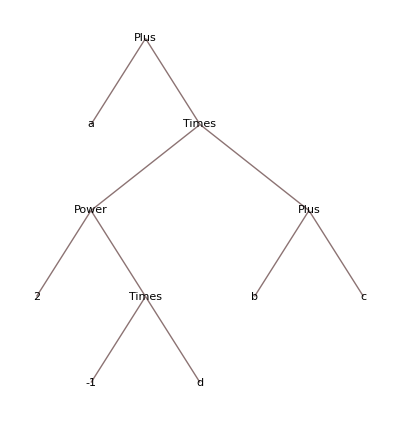

```mathematica
TreeForm[a+(b+c)/2^d]
```

```mathematica
(*atomic expression*)
```

```mathematica
Symbol
```

Symbol

```mathematica
Number
```

Number

```mathematica
String
```

String

```mathematica
gy= {1,2,3,4}
```

{1,2,3,4}

```mathematica
FullForm[Unevaluated[gy= {1,2,3,4}]]
```

Unevaluated[Set[gy,List[1,2,3,4]]]

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
FullForm[Unevaluated[1+2+3]]
```

Unevaluated[Plus[1,2,3]]

```mathematica
(*Apply @@*)
(*
fff@@ggg[a1,a2,...,aN] ---> fff[a1,a2,....aN]
*)
(*prefix form*)
(*
fff@ggg[a1,a2,...,aN] ---> fff[ggg[a1,a2,...,aN]]
*)
```

```mathematica
gy
```

{1,2,3,4}

```mathematica
Head@l
```

List

```mathematica
Apply[Plus,gy]
```

10

```mathematica
Plus@@gy
```

10

```mathematica
Length@gy
```

4

```mathematica
Length[1+2+3]
```

0

```mathematica
Length[Unevaluated[1+2+3+5]]
```

4

```mathematica
gy[[1]]
```

1

```mathematica
gy[[0]]
```

List

```mathematica
(1+2+3)[[0]]
```

Integer

```mathematica
Unevaluated[1+2+3][[0]]
```

Plus

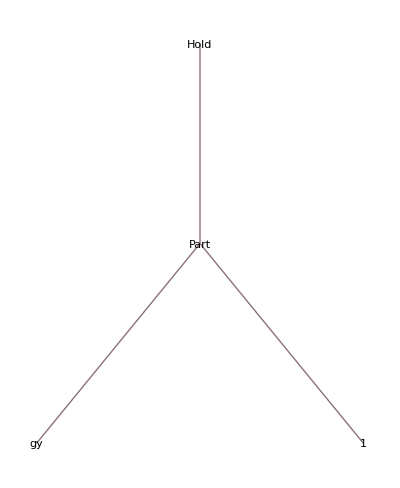

```mathematica
TreeForm[Hold[gy[[1]]]]
```

```mathematica
FullForm[Hold[gy[[1]]]]
```

Hold[Part[gy,1]]

```mathematica
Sin[1]
```

Sin[1]

```mathematica
(* 
 f=...
Не работает
fprime[x_]:=D[f[x],x];

Нормально
fprime[x_]=D[f[x],x];
*)
```

```mathematica
Attributes
```

Attributes

```mathematica
Attributes[FullForm]
```

{Protected}

```mathematica
FullForm[Set[a,5]]
```

5

```mathematica
FullForm[Unevaluated[a:=5]]
```

Unevaluated[SetDelayed[a,5]]

```mathematica
Attributes[Set]
```

{HoldFirst,Protected,SequenceHold}

```mathematica
(*head[Не обрабатывать arg1, arg2, ....]*)
```

```mathematica
Attributes[SetDelayed]
(*head[Не обрабатывать arg1, Не обрабатывать arg2, ....]*)
```

{HoldAll,Protected,SequenceHold}

```mathematica
a=123
```

123

```mathematica
a=RandomInteger[{1,10}]
```

```mathematica
6
(*HoldFirst Set*)
```

```mathematica
a1:=RandomInteger[{1,10}]
(*HoldFirst SetDelayed*)
```

```mathematica
a1
```

8

```mathematica
Attributes[FullForm]
```

{Protected}

```mathematica
Unprotect[FullForm]
```

{FullForm}

```mathematica
SetAttributes[FullForm, HoldFirst]
```

```mathematica
FullForm[1+2+3]
```

Plus[1,2,3]

```mathematica
Sin[{1,2,3,4}]
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
f[n_]:={#,Mean[#], Variance[#]}&@RandomInteger[{1,10},n]
```

```mathematica
f[2]
```

{{8,9},17/2,1/2}

```mathematica
f[{2,3,4}]
```

{{{{7,5,2,6},{4,4,8,3},{9,5,2,8}},{{4,8,5,3},{2,2,7,9},{7,3,4,10}}},{{11/2,13/2,7/2,9/2},{3,3,15/2,6},{8,4,3,9}},{{9/2,9/2,9/2,9/2},{2,2,1/2,18},{2,2,2,2}}}

```mathematica
Attributes[f]
```

{}

```mathematica
SetAttributes[f,Listable]
```

```mathematica
f[{2,3,4}]
```

{{{6,8},7,2},{{2,7,5},14/3,19/3},{{9,8,8,1},13/2,41/3}}

```mathematica
roots=Solve[x^5==1,x]
```

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}